```mathematica
(*Computer Graphics with Applications of Dr.Makhanov.
Lab 3
"Flying" Objects and Rotations.*)
```

```mathematica
(*Part 1*)
```

```mathematica
(*Circle,radius 3 and the center at {1,1} use Graphics*)
```

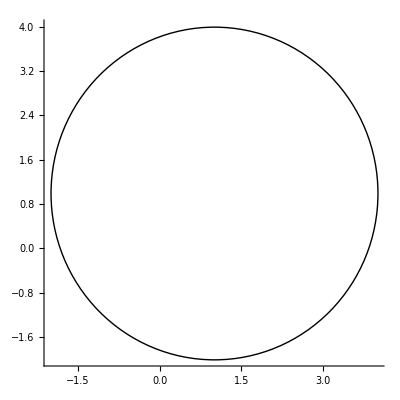

```mathematica
Graphics[Circle[{1,1},3],Axes->True,ImageSize->Tiny]
```

```mathematica
(*Sphere radius 2 and the center at {1,1,1} use Graphics 3D*)
```

```mathematica
Graphics3D[Sphere[{1,1,1},2],Axes->True,ImageSize->Tiny]
```

-Graphics3D-

```mathematica
(*Cube,centered at {1,1,1} with the side 4*)
```

```mathematica
Graphics3D[Cube[{1,1,1},4],Axes->True,ImageSize->Tiny,PlotRange->{{-5,5},{-5,5},{-5,5}}]
```

-Graphics3D-

```mathematica
(*Problem1*)
```

```mathematica
x1[t_] := Cos[7t]Cos[11t]
```

```mathematica
y1[t_] := Cos[7t]Sin[11t]
```

```mathematica
p1[t_] := {x1[t],y1[t]}
```

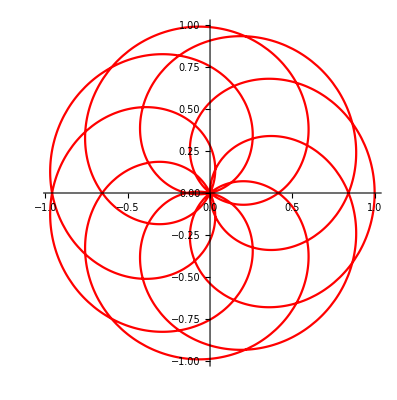

```mathematica
plotg1 = ParametricPlot[p1[t],{t,0,Pi},PlotStyle->Red]
```

```mathematica
plot1[s_] := ParametricPlot[p1[t],{t,0,s},PlotStyle->Red,PlotRange->{{-1,1},{-1,1}},PlotPoints->100]
```

```mathematica
Manipulate[plot1[s],{s,0.1,Pi,0.1}]
```

```mathematica
(*Problem2*)
```

```mathematica
Rss:=0.25
```

```mathematica
plot2[s_]:=Graphics[{Blue,Thick,Circle[p1[s],Rss]},PlotRange->{{-1,1},{-1,1}},Axes->True]
```

```mathematica
Manipulate[plot2[s],{s,0.1,Pi,0.001}]
```

```mathematica
plot1and2[s_] := Show[plot2[s],plotg1]
```

```mathematica
Manipulate[plot1and2[s],{s,0.1,Pi,0.001}]
```

```mathematica
(*Problem3*)
```

```mathematica
data3={{-3,-1},{-1,-2},{1,-2},{2,-3},{1,-4},{-1,-4},{-2,-5},{-2,-6},{-1,-6},{-1,-5},{2,-5},{3,-4},{6,-5},{7,-7},{6,-8},{6,-9},{7,-9},{7,-8},{8,-7},{7,-4},{6,-4},{6,-2},{5,0},{10,-1},{7,0},{10,0},{7,1},{10,2},{8,2},{10,3},{6,2},{5,0},{3,0},{1,2},{1,3},{-2,6},{-3,6},{-4,7},{-4,6},{-6,4},{-6,3},{-5,3},{-3,4},{-2,2},{-3,1},{-5,2},{-7,0},{-7,-1},{-6,-1},{-6,0},{-5,1},{-4,0},{-5,-2},{-3,-4},{-2,-4},{-2,-3},{-3,-3},{-4,-2},{-3,-1}};
```

```mathematica
x3 = Transpose[data3][[1]]
```

{-3,-1,1,2,1,-1,-2,-2,-1,-1,2,3,6,7,6,6,7,7,8,7,6,6,5,10,7,10,7,10,8,10,6,5,3,1,1,-2,-3,-4,-4,-6,-6,-5,-3,-2,-3,-5,-7,-7,-6,-6,-5,-4,-5,-3,-2,-2,-3,-4,-3}

```mathematica
y3 = Transpose[data3][[2]]
```

{-1,-2,-2,-3,-4,-4,-5,-6,-6,-5,-5,-4,-5,-7,-8,-9,-9,-8,-7,-4,-4,-2,0,-1,0,0,1,2,2,3,2,0,0,2,3,6,6,7,6,4,3,3,4,2,1,2,0,-1,-1,0,1,0,-2,-4,-4,-3,-3,-2,-1}

```mathematica
sx3= Interpolation[x3]
```

InterpolatingFunction[…]

```mathematica
sy3 = Interpolation[y3]
```

InterpolatingFunction[…]

```mathematica
s3[t_] := {sx3[t],sy3[t]}
```

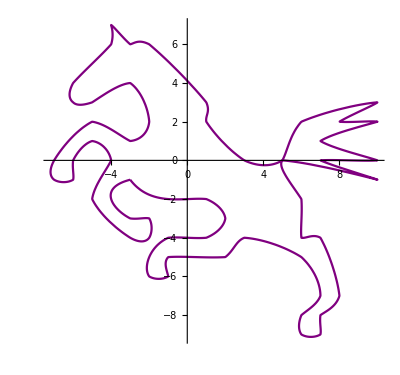

```mathematica
plot31 = ParametricPlot[s3[t],{t,1,Length[x3]},PlotStyle->Purple]
```

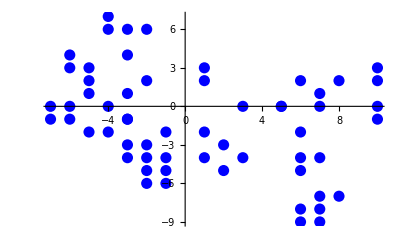

```mathematica
plot32 = ListPlot[data3,PlotStyle->{Blue,PointSize[0.02]}]
```

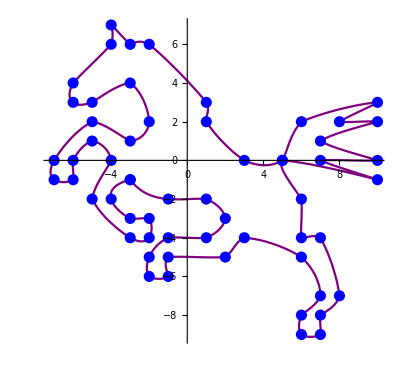

```mathematica
Show[plot31,plot32]
```

```mathematica
(*Problem4*)
```

```mathematica
Rs4:=1.0
```

```mathematica
pplot4[s_]:=Graphics[{Red,Thick,Circle[s3[s],Rs4]},PlotRange->{{-10,10},{-10,10}},Axes->True]
```

```mathematica
plot41[s_] := Show[pplot4[s],plot31]
```

```mathematica
Manipulate[plot41[s],{s,1,Length[x3]}]
```

```mathematica
(*Problem5*)
```

```mathematica
data5={{1,1,1},{2,3,1},{1,3,2},{4,3,3},{4,4,7},{5,3,2},{7,5,6},{5,5,5}}
```

{{1,1,1},{2,3,1},{1,3,2},{4,3,3},{4,4,7},{5,3,2},{7,5,6},{5,5,5}}

```mathematica
x5 = Transpose[data5][[1]]
```

{1,2,1,4,4,5,7,5}

```mathematica
y5 = Transpose[data5][[2]]
```

{1,3,3,3,4,3,5,5}

```mathematica
z5 = Transpose[data5][[3]]
```

{1,1,2,3,7,2,6,5}

```mathematica
sx5 = Interpolation[x5]
```

InterpolatingFunction[…]

```mathematica
sy5 = Interpolation[y5]
```

InterpolatingFunction[…]

```mathematica
sz5 = Interpolation[z5]
```

InterpolatingFunction[…]

```mathematica
s5[t_] :={sx5[t],sy5[t],sz5[t]}
```

```mathematica
plot5 = ListPointPlot3D[data5,PlotStyle->PointSize[0.05]]
```

-Graphics3D-

```mathematica
plotg5 = ParametricPlot3D[s5[t],{t,1,Length[x5]},PlotStyle->{Red,Thick}]
```

-Graphics3D-

```mathematica
Show[plotg5,plot5]
```

-Graphics3D-

```mathematica
(*Problem6*)
```

```mathematica
Rs6 = 0.8
```

0.8

```mathematica
plotc6[s_] := Graphics3D[Sphere[s5[s],Rs6],PlotRange->{{0,8},{0,8},{0,7}}]
```

```mathematica
plot6show[s_]:=Show[{plotc6[s],plotg5,plot5},PlotRange->{{0,8},{0,8},{0,9}}]
```

```mathematica
Manipulate[plot6show[s],{s,1,8,0.5}]
```

```mathematica
(*Problem7*)
```

```mathematica
smax=20
```

20

```mathematica
Rs7 = 0.5
```

0.5

```mathematica
R7=1.5
```

1.5

```mathematica
x7[t_]:=R7*Cos[t]
```

```mathematica
y7[t_]:=R7*Sin[t/1.2]
```

```mathematica
z7[t_]:=t/5
```

```mathematica
trajectory7[t_]:={x7[t],y7[t],z7[t]}
```

```mathematica
plotg7=ParametricPlot3D[trajectory7[t],{t,0,smax}]
```

-Graphics3D-

```mathematica
plot7[s_]:=Graphics3D[{Blue,Sphere[trajectory7[s],Rs7]},PlotRange->{{-2,2},{-2,2},{-1.5,5}},Axes->True]
```

```mathematica
plotshow7[s_]:=Show[plot7[s],plotg7]
```

```mathematica
Manipulate[plotshow7[s],{s,0,smax,0.001}]
```

```mathematica
(*Part2*)
```

```mathematica
(*Problem8*)
```

```mathematica
(*Problem9*)
```

```mathematica
(*Problem10*)
```

```mathematica
(*Problem11*)
```

```mathematica
(*Bonus_Problem12*)
```

```mathematica
(*Bonus_Problem13*)
```